# Physicist's Introduction to Mathematica 6

## Third Edition 2007

## PHYSICS 200

Nicholas Wheeler

REED COLLEGE

NOTE: The first editionof this material, written during the summer of 2000, was designed in the presumption that Mathematica 4 would be running on Macintosh OS 9. By the summer of 2006 Mathematica had acquired new capabilities, and OS X had become commonplace. My 2nd edition, intended to take into account those developments, was written in the presumption that Mathematica 5.2 would be running on OS X version 10.4 or a comparable system.

Now Mathematica 6 has appeared, which has new capabilities, but has been stripped of many of the features most characteristic of  Mathematica 5.2. The differences are so great that notebooks written in 5.2 typically will not run (or at least will not run smoothly) on 6. I have been obliged to start once again, from scratch.

## Laboratory 0

## Why Bother to Learn Mathematica?

Until a few years ago my own response to that question would have been "Why indeed? I became a physicist in order to learn some things about how Nature works, not things about v.6 of some proprietary software…described in a book thicker and heavier than any of my physics books!" But the fact of the matter is that we probe Nature not with our bare hands, but with tools—man-made contrivances, whether we call them principles, theorems, analytical techniques or multi-channel analyzers. So the short answer is: Because Mathematica is a wonderful new tool—sharper and more broadly useful than most others that spring to mind, and remarkably easy to use.

Mathematica, first released in June 1988, is a creation of Stephen Wolfram (born in 1959).  It provides an almost exhaustive compendium of mathematical data and information, and a computing engine of such immeasurably broad potential that few can claim mastery of all its parts…which is why The Mathematica Book is so thick, and why so much supplemental material (books, downloadable software) treating this or that special area of application have come into being. Let us therefore accept at the outset that our present objective must be a limited one—to gain a working familiarity with the elementary first principles of Mathematica, and some rough sense of its potential.  Refined procedures we agree to reserve for the day when the work at hand requires that we move beyond the basics, and lends urgency to the effort.

It will very soon become apparent to you that Mathematica is so powerful—and so easy to control—that it opens a door to quick-and-easy mathematical experimentation that until now has stood shut even to the greatest minds—a door to an entirely new and much more improvisatory way of thinking about and doing pure & applied mathematics.  You will find yourself in position to do things that formerly you would not even have dreamed of doing (certainly not of doing casually, without a lot of labor-intensive special-purpose programming), and that the formulation/testing of conjectures has come to occupy a central position in your mathematical life.

## Getting Started…and Stopped

I begin with a cautionary word: It is inevitable that you will from time to time (and especially in the beginning) steer Mathematica off the road, and have to Restart.  To avoid catastrophy

Be sure that you have Saved open  documents running in other applications.

Mathematica comes in two large and semi-autonomous packages:

• the computing engine itself, called the "kernel";

• the "front end", which mediates the flow of information between you and the kernel (or perhaps several kernels, running simultaneously on several computers). The front end manages screen display, graphics, access to the Documentation Center (which in Mathematica 6 replaces the "Browser," and is where one goes for assistance) and much else, and can perform certain tasks independently of the kernel; it was originally conceived and designed not by Wolfram himself, but by Theodore Gray.

You already have the front end running (may have turned it on by selecting and double-clicking Mathematica 6 in your Applications folder). To turn on the kernel and (more to the point) to establish communication between the front end and the kernel the traditional procedure is to type 2-2 and hit ENTER:

```mathematica
2-2
```

0

NOTE: The traditional procedure is to type 2+2. The advantage of my eccentric 2-2 procedure is that it can be done with one hand, without use of the SHIFT key.

That took several seconds—a long time by the standard to which you will become accustomed, because the kernel is fat. Note that, while the kernel was performing its work your input acquired an input number, and the output (when at last it appeared) was assigned a corresponding output number.

To experience the often blinding speed of Mathematica, try

```mathematica
1000!
```

402387260077093773543702433923003985719374864210714632543799910429938512398629020592044208486969404800479988610197196058631666872994808558901323829669944590997424504087073759918823627727188732519779505950995276120874975462497043601418278094646496291056393887437886487337119181045825783647849977012476632889835955735432513185323958463075557409114262417474349347553428646576611667797396668820291207379143853719588249808126867838374559731746136085379534524221586593201928090878297308431392844403281231558611036976801357304216168747609675871348312025478589320767169132448426236131412508780208000261683151027341827977704784635868170164365024153691398281264810213092761244896359928705114964975419909342221566832572080821333186116811553615836546984046708975602900950537616475847728421889679646244945160765353408198901385442487984959953319101723355556602139450399736280750137837615307127761926849034352625200015888535147331611702103968175921510907788019393178114194545257223865541461062892187960223838971476088506276862967146674697562911234082439208160153780889893964518263243671616762179168909779911903754031274622289988005195444414282012187361745992642956581746628302955570299024324153181617210465832036786906117260158783520751516284225540265170483304226143974286933061690897968482590125458327168226458066526769958652682272807075781391858178889652208164348344825993266043367660176999612831860788386150279465955131156552036093988180612138558600301435694527224206344631797460594682573103790084024432438465657245014402821885252470935190620929023136493273497565513958720559654228749774011413346962715422845862377387538230483865688976461927383814900140767310446640259899490222221765904339901886018566526485061799702356193897017860040811889729918311021171229845901641921068884387121855646124960798722908519296819372388642614839657382291123125024186649353143970137428531926649875337218940694281434118520158014123344828015051399694290153483077644569099073152433278288269864602789864321139083506217095002597389863554277196742822248757586765752344220207573630569498825087968928162753848863396909959826280956121450994871701244516461260379029309120889086942028510640182154399457156805941872748998094254742173582401063677404595741785160829230135358081840096996372524230560855903700624271243416909004153690105933983835777939410970027753472000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

REMARK: If you SELECT the bracket that embraces both input and output, and then double-click, the output will disappear from view and a down-pointing arrow will appear on the right. Select and double-click again to make the output reappear. Try it!

```mathematica
Expand[(1+x)^100]
```

1+100 x+4950 x^2+161700 x^3+3921225 x^4+75287520 x^5+1192052400 x^6+16007560800 x^7+186087894300 x^8+1902231808400 x^9+17310309456440 x^10+141629804643600 x^11+1050421051106700 x^12+7110542499799200 x^13+44186942677323600 x^14+253338471349988640 x^15+1345860629046814650 x^16+6650134872937201800 x^17+30664510802988208300 x^18+132341572939212267400 x^19+535983370403809682970 x^20+2041841411062132125600 x^21+7332066885177656269200 x^22+24865270306254660391200 x^23+79776075565900368755100 x^24+242519269720337121015504 x^25+699574816500972464467800 x^26+1917353200780443050763600 x^27+4998813702034726525205100 x^28+12410847811948286545336800 x^29+29372339821610944823963760 x^30+66324638306863423796047200 x^31+143012501349174257560226775 x^32+294692427022540894366527900 x^33+580717429720889409486981450 x^34+1095067153187962886461165020 x^35+1977204582144932989443770175 x^36+3420029547493938143902737600 x^37+5670048986634686922786117600 x^38+9013924030034630492634340800 x^39+13746234145802811501267369720 x^40+20116440213369968050635175200 x^41+28258808871162574166368460400 x^42+38116532895986727945334202400 x^43+49378235797073715747364762200 x^44+61448471214136179596720592960 x^45+73470998190814997343905056800 x^46+84413487283064039501507937600 x^47+93206558875049876949581681100 x^48+98913082887808032681188722800 x^49+100891344545564193334812497256 x^50+98913082887808032681188722800 x^51+93206558875049876949581681100 x^52+84413487283064039501507937600 x^53+73470998190814997343905056800 x^54+61448471214136179596720592960 x^55+49378235797073715747364762200 x^56+38116532895986727945334202400 x^57+28258808871162574166368460400 x^58+20116440213369968050635175200 x^59+13746234145802811501267369720 x^60+9013924030034630492634340800 x^61+5670048986634686922786117600 x^62+3420029547493938143902737600 x^63+1977204582144932989443770175 x^64+1095067153187962886461165020 x^65+580717429720889409486981450 x^66+294692427022540894366527900 x^67+143012501349174257560226775 x^68+66324638306863423796047200 x^69+29372339821610944823963760 x^70+12410847811948286545336800 x^71+4998813702034726525205100 x^72+1917353200780443050763600 x^73+699574816500972464467800 x^74+242519269720337121015504 x^75+79776075565900368755100 x^76+24865270306254660391200 x^77+7332066885177656269200 x^78+2041841411062132125600 x^79+535983370403809682970 x^80+132341572939212267400 x^81+30664510802988208300 x^82+6650134872937201800 x^83+1345860629046814650 x^84+253338471349988640 x^85+44186942677323600 x^86+7110542499799200 x^87+1050421051106700 x^88+141629804643600 x^89+17310309456440 x^90+1902231808400 x^91+186087894300 x^92+16007560800 x^93+1192052400 x^94+75287520 x^95+3921225 x^96+161700 x^97+4950 x^98+100 x^99+x^100

That was fast. Some calculations, of course, take longer—maybe much longer. Occasionally it is of interest to know how long it took Mathematica to perform a given calculation. To provide that information, Mathematica provides the command Timing. To learn about that command one proceeds as one proceeds to learn about any command: enter the command

```mathematica
?Timing
```

RowBox[{"Timing", "[", StyleBox["expr", "TI"], "]"}] evaluates StyleBox["expr", "TI"], and returns a list of the time in seconds used, together with the result obtained.

To obtain more detailed information, and to see examples, double click on the ≫.

To illustrate use of the Timing command I provide now an example of a calculation that takes about 15 seconds to perform. Notice that while the Kernel is busy with the calculation the word Running appears at the top of the page. If you enter additional commands while the Running flag flys, the Kernel will read/execute them in sequence after it has completed its present work.

```mathematica
cornu[t_]:={∫_0^t Sin[u^2]ⅆu,∫_0^t Cos[u^2]ⅆu}
```

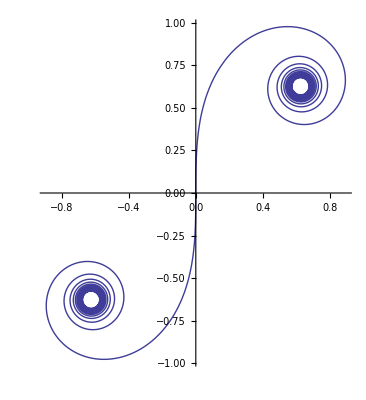
{15.3986,-Graphics-}

```mathematica
ParametricPlot[Evaluate[cornu[t]],{t,-10,10},
AspectRatio->Automatic]//Timing
```

That pretty figure shows the Cornu spiral, which acquires importance in physical optics (diffraction theory).

### Terminating a Running Calculation

Not infrequently you will want, for one reason or another, to terminate a calculation. Maybe you've realized you have asked Mathematica to do the wrong thing, or the calculation has run so long that you suspect (unfortunately, Mathematica returns no progress reports) something may be wrong with your command, or Mathematica reports back that it has been caught up in an endless loop. In such cases the first thing to try is

⌘.  Simple abort: hold down ⌘ and press period…and wait.

Equivalently, you might select Abort Evaluation from the front end's Evaluation menu.The kernel has to "back up," so the wait is roughly proportional to how deep you were into the calculation, but eventually (after perhaps several seconds or minutes) an Out[#]=Aborted should appear.

But Mathematica, once started, reveals a single-minded reluctance to quit, and after a long wait you may conclude that the simple technique just described is not going to work. Or perhaps you are simply tired of waiting. Try

Evaluation > Quit Kernel

or

⌘q  Simple quit Mathematica: you will be asked if you want to Save your work,

then both the front end and the kernel will shut down, and you will have to Restart the application. If that is ineffective, try hitting

⌘⌥Esc Hard dump of the kernel. Save your work, Quit Mathematica, Restart.

Finally, you can turn off the computer (a "forced quit" may be necessary) or, in dire cases, unplug the computer…but will lose any unsaved open documents. It is in anticipation of such an event (or other misfortune) that you should be careful to

Save your notebook at frequent intervals.

SUGGESTION: WRITE THOSE ALTERNATIVE TERMINATION METHODS DOWN ON A SLIP OF PAPER. For when you most need them you will not be able to access this notebook (or any other source) where they are described.

## Notebooks

Mathematica documents are called "notebooks," and wear the suffix .nb  Open the File menu, select New (alternatively: hit ⌘n), and you have created a new notebook.  Use File > Save As… (alternatively: ⇧⌘s) to name and save the notebook.

Notebooks can be rendered in various "styles"—designs intended for different uses. Mathematica 6 is shipped with 17 canned designs: open Format > Stylesheet to see the list and sublists.  Try them, one after the other, to see what they do to this text, which I have written (and  prefer to have read) in Book > Textbook style.

Different canned styles come equipped with different sets of options—few in some cases, numerous in others. Open Window, note the control options placed thus at your disposal, and activate Show Toolbar. Select the Default style, and open the ToolBar menu: it shows only a few options. Now return to Textbook Style: it shows dozens of options…which is one (but only one) of the reasons I have elected to work in that style.

Under Format you find Edit Stylesheet, and someday you may have occasion to do just that.  But for the moment we have already in hand all the resources we will need. My general advice:

• Mathematica is intolerant of typos—all capitalization, every brace and bracket (whether round, curly or square), every bit of punctuation must be exactly right—so work with the magnification (adjustable at the bottom of the page) big enough that you can clearly distinguish . from , etc.

• Show the Toolbar; it is a great aid to the insertion of section titles, explanatory text, etc.

• Make the page large, yet small enough to leave room on the screen for an input pallet or two.

• At the beginning of each work session your first command will cause Mathematica to attempt automatically to open the Kernel, but if the command is complicated that attempt may take long time, or even fail. Always start with a simple command, like the classic evaluation of 2-2.

For access to a lot of useful information about this broad topic and the topic  addressed below, go to Documentation Center and search for tutorial/InputAndOutputInNotebooksOverview.

## Input Techniques &Tips

Mathematica assigns distinct and non-interchangeable responsibilities to ( ), [ ] and { }. Those I will explain in a moment. But first a

TIP: The correct way to type (stuff) is not to type ( then stuff then ) but

( )  then the stepleft key ← then  stuff and finally  the stepright key →

That way, having typed a (,  you will avoid both the danger of forgetting or misplacing the ), and will avoid also the distraction of Mathematica's signal that it has detected an unclosed parenthetic. A similar remark pertains—for the same reasons—to running TEX…and, indeed, to all electronic keyboard work.

• Mathematica reserves ( ) to delimit expressions, as in (1+x)^n and (a+b)(c+d).

• Mathematica reserves [ ] to identify the arguments of functions, where the term "function" is (as will emerge) very broadly construed; simple examples are f[x,y] and Sin[x].

• Mathematica reserves { } to identify lists, where again the term will be very broadly construed; thus {2,3,5,7,11,13} is a list of primes, and {{a,b},{c,d}} is a list of lists (i.e., a matrix):

```mathematica
{{a,b},{c,d}}//MatrixForm
```

(a | b
c | d)

### Palettes

Versions 1 (1988) and 2 (1991) of Mathematica required one to communicate with the front end in a kind of one-dimensional "telegraphic" code.  For example, to evaluate  ∫_0^∞ x e^(-x^3)dx one had to enter

```mathematica
Integrate[x Exp[-x^3],{x,0,Infinity}]
```

1/3 Gamma[2/3]

That, as you see, still works, and is the style still preferred by some people. It is—in simple contexts—often the quickest way to go, but never pretty. For many commands the telegraphic style remains mandatory in Version 6; look, for example—picking one from a zillion—to the following command:

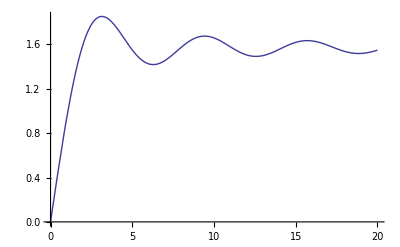

```mathematica
Plot[SinIntegral[x], {x,0,20},PlotRange->All]
```

But—beginning with Version 3 (1996) and continuing with Versions 4 (1999), 5 (2005) and 6 (2007)—it has become possible to enter many commands using a "two-dimensional" code that looks much like ordinary mathematical notation you use when working by hand or create when writing in TEX. Returning to our recent example: to evaluate ∫_0^∞ x e^(-x^3)dx one might use the BasicMathInput palette (of which more in a minute) to construct the command

```mathematica
∫_0^∞ x ⅇ^(-x^3)ⅆx
```

1/3 Gamma[2/3]

which, as you see, functions exactly like its telegraphic counterpart. The standard collection serves most needs, but can readily be expanded by the user who has specialized requirements.

The Palettes menu leads you to a selection of six pallets listed above the line (I will have nothing to say about the advanced options below the line, or the procedure you can use to construct palettes that serve your specialized needs). Open each, to get a rough sense of the lay of the land. The AlgebraicManipulation palette provides quick access to common commands we will soon commit to memory, so is of relatively little use. Of especially high utility is the BasicMathInput palette, which you will often want to have available in some handy position on your computer screen. Also of very frequent use are the resources of the SpecialCharacters palette, which is seen to be really a collection of twelve palettes: Palettes > SpecialCharacters and Insert > SpecialCharacter... serve equally well to get you there.

Concerning the BasicMathInput, a CAUTIONARY WARNING is in order, for Mathematica 6 has in this connection developed an unfortunate quirk. Suppose we are working in "Textbook" style, and (because we went Window > ✓ Show Toolbar at the beginning of this work session) have the "Toolbar" showing (which is always a good idea). Suppose, moreover, that—having placed ourselves in the Input mode—we propose to use the BasicMathInput to write

```mathematica
∫□ⅆ□
```

We are astounded to discover that the symbol actually created by the "integrate" button looks like this

# ∫□ⅆ□

and that Mathematica has flipped spontaneously into "Title" mode. To create the symbol we intended, and to get on with writing out intended command, we have to return to the Toolbar and—by hand—flip back into Input mode. It turns out that this disease is present only when the BasicMathInput palette is being used to creat the first symbol of a command: no problem arises if the palette is used to create subsequent symbols. We can use that circumstant to construct a WORKAROUND: To create (say)

```mathematica
∫□ⅆ□
```

first type (say)

```mathematica
q∫□ⅆ□
```

and then erase the q. Alternatively (and just as quickly) one can avoid the problem altogether by using the keyboard (in the manner discussed below) to create 2-dimensional symbols. For  example, one has only to type EscinttEsc to create

```mathematica
∫□ⅆ□
```

What distinguishes the ■ boxes from the □ boxes that are evident on the BasicMathInput palette? The answer is made obvious by example. If you were to enter

```mathematica
x^2+Sin[x]
```

as Input, then to Select that expression and to hit the ∫■ⅆ□ button, the expression would go inside the ■, producing

```mathematica
∫(x^2+Sin[x])ⅆ□
```

Now place the cursor on □, type x and get

```mathematica
∫(x^2+Sin[x])ⅆx
```

x^3/3-Cos[x]

Similarly, we might type and Select ■^□ button, on the other hand, gives

```mathematica
1+√(1+(a+x)/b)
```

and then hit the ■^□ button to obtain

```mathematica
(1+√(1+(a+x)/b))^□
```

which, after entering a 3 into the □ becomes

```mathematica
(1+√(1+(a+x)/b))^3
```

Our final example makes clear the fact that in some contexts ■ distinguishes the box into which the next keystroke will be inserted (Mathematica manuals often call ■ the "SelectionPlaceholder," and □ simply "a Placeholder"). We have interest in a 5× 7 matrix, so go Insert > Table/Matrix > New and, by selection the appropriate options, create

```mathematica
({{□, □, □, □, □, □, □}, {□, □, □, □, □, □, □}, {□, □, □, □, □, □, □}, {□, □, □, □, □, □, □}, {□, □, □, □, □, □, □}})
```

Placing the cursor on □ the in the upper left corner, we type a⇥b⇥c↓d↓e↓f⇥g⇥h↑i⇥j to create

```mathematica
({{a, b, c, □, □, □, □}, {□, □, d, □, □, □, □}, {□, □, e, □, i, j, □}, {□, □, f, g, h, □, □}, {□, □, □, □, □, □, □}})
```

This illustrates how (very commonly) ⇥ and (less commonly) ↓, ↑, ← and → are used to adjust the location of the box ■ that will receive the next keystroke.

### Creating 2-Dimensional Commands & Special Symbols at the Keyboard

Palette buttons are a great aid to speed and legibility.  But they require use of the mouse, and in some situations their repetitive use can become tedious (though deft use of Cut/Copy/Paste often permits accelerated escape from the tedium). It is useful to know that the action of palette buttons can often be achieved directly from the keyboard. Open Palettes > SpecialCharacters, then open (say) Technical Symbols. Click on (say) ⅇ and see a "double struck e." Mathematica considers "e"  to be simply a letter, and uses the "double struck e" to denote the base of the natural logarithms, with numerical value

```mathematica
N[ⅇ]
```

2.71828

The palette informs you, if you click on the letter "e", that you can produce ⅇ at the point identified by the blinking cursor either (1) by selecting ⅇ on the palette and hitting the Insert button, or (2) by typing EsceeEsc. Similarly

ℏ can be produced by EschbEsc

∞ can be produced by EscinfEsc

ⅈ can be produced by EsciiEsc

Etc. Not all of the special characters can be produced in this way, but most of the most commonly encountered ones can be, and the palettes tell you which can (and how), which can't. Notice in this connection that the

π produced by EscpEsc, else by the Greek Letters palette

functions simultaneously as a letter and as a mathematical constant:

```mathematica
N[π]
```

On the other hand, the letter "i" is always just a letter: the square root of minus one is always double struck:

```mathematica
√-1
```

ⅈ

Relatedly, "capital I"—when it occurs as stand-alone input—is a "Protected Symbol," which is always interpreted to mean a complex number:

```mathematica
N[I]
```

0.+1. ⅈ

Similarly protected are C, E and N.

Here is a short list of keyboard commands that produce important mathematical symbols:

Esc*Esc produces ×

EsccrossEsc produces ×

Esc!=Esc produces ≠

Esc===Esc produces ≡

Esc<=Esc produces ≤

Esc>=Esc produces ≥

EscelemEsc produces ∈ (meaning "is an element of")

EscintEsc produces ∫

EscinttEsc produces ∫□ⅆ□

EscdinttEsc produces ∫_□^□ □ⅆ□

EscsumtEsc produces ∑_(□=□)^□ □

EscprodtEsc produces ∏_(□=□)^□ □

EscdEsc produces ∂

EscdtEsc produces ∂_□ □

Ctrl-2 produces √□

The prefix "ds" produces "double struck"  upper/lower case letters:

EscdsAEsc produces 𝔸

EscdsaEsc produces 𝕒

EscdsBEsc produces 𝔹

EscdsbEsc produces 𝕓

The prefix "go" produces "Gothic"  upper/lower case letters;

The prefix "sc" produces "script" upper/lower case letters.

The relevant SpecialCharacters palette shows what those look like, and you are in position now to construct them for yourself, so I provide no samplers.

It was easy to obtain such information in Mathematica 5, is less easy in Mathematica 6. But if you go Help > Documentation Center and launch a search for tutorial/EnteringTwoDimensionalExpressionsOverview you will find links that take you to discussions of various specialized aspects of this subject. Or—more quickly—visit .

## Three Primary Flavors of =

Enter the following:

```mathematica
?=
?:=
?==
```

lhs=rhs evaluates rhs and assigns the result to be the value of lhs. From then on, lhs is replaced by rhs whenever it appears. 
{l_1,l_2,…}={r_1,r_2,…} evaluates the r_i, and assigns the results to be the values of the corresponding l_i.

RowBox[{StyleBox["lhs", "TI"], ":=", StyleBox["rhs", "TI"]}] assigns StyleBox["rhs", "TI"] to be the delayed value of StyleBox["lhs", "TI"]. StyleBox["rhs", "TI"] is maintained in an unevaluated form. When StyleBox["lhs", "TI"] appears, it is replaced by StyleBox["rhs", "TI"], evaluated afresh each time.

RowBox[{StyleBox["lhs", "TI"], "==", StyleBox["rhs", "TI"]}] returns True if StyleBox["lhs", "TI"] and StyleBox["rhs", "TI"] are identical.

What, in plain words, do those statements mean?

### Assignment

Mathematica understands that when we write

```mathematica
a=2
```

2

we are assigning the meaning/value 2 to the symbol a. So we have

```mathematica
a+1
```

3

If we now write

```mathematica
a=Sin[x]
```

Sin[x]

we have reassigned meaning to a:

```mathematica
1-a^2
Simplify[%]
```

1-Sin[x]^2

Cos[x]^2

```mathematica
Clear[a]
```

When we write

```mathematica
g=Plot[x Sin[x],{x,0,100}];  (*The semi-colon says to Mathematica "Don't show the figure"*)
```

we have, in effect, asserted that g will be the name of a graph. Here is an instance of the use of that name:

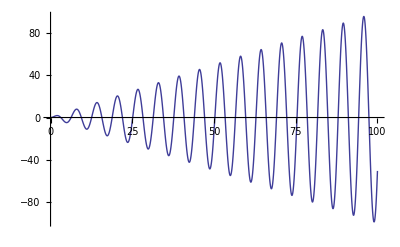

```mathematica
Show[g]
```

A mnemonically better name in this instance might have been something like

```mathematica
firstgraph=Plot[x Sin[x],{x,0,100}];
Show[firstgraph]
```

-Graphics-

It was to permit the practice of giving variables/functions/graphs such easily remembered (if long-winded) names that the designers of Mathematica interpret xy to be a compound symbol or "name," and require use of some special device to signify "multiplication":

x y Here the ␣ signifies multiplication; alternatively, use

x*y or  x×y where ×, as we have seen, is produced Esc*Esc. But beware: it will emerge that one must write

x.y if  x and y are matrices that you intend to multiply.

Conversely, spaces cannot be used in names.

It is permitted to make several assignments simultaneously. Try

```mathematica
p=Tom
q=Dick
r=Harry
```

Tom

Dick

Harry

Notice that a single input (see the cell-bracket on the right) has produced three lines of output. Now, as a test, try

```mathematica
List[p,q,r]
Clear[p,q,r] (*This housekeeping detail as been built right into the command, since List is the last thing we plan to do with p q and r*)
```

{Tom,Dick,Harry}

```mathematica
List[p, q, r]
```

{p,q,r}

REMARK: This is as good a point as any to see what the Documentation Center has to say about the important concept of a "List."  To that end, enter the command

```mathematica
?List
```

Be sure to click on the ≫.

### Delayed Assignment: Functional Definition

Were we to write

```mathematica
f=x^3
```

x^3

(thus giving the name  f to the expression on the right) we would—for some limited purposes—be in position to treat  f  as though it were a  function; try

```mathematica
D[f, x]
∫fⅆx
```

3 x^2

x^4/4

```mathematica
Clear[f]
```

But we would not be in position to ask "What is the value assumed by  f  at  x = 3 ?" Or to plot  f(x) .  Mathematica understands

```mathematica
f[x_]:=x^3
```

(note the presence of the colon) to signify that we intend to delay the assignment of specific value to x; in short, to look upon the preceding command as a description of the functional structure we have assigned to  f[x].  We are only now in position to make commands such as the following:

27

{1,8,27}

1+6 x^5

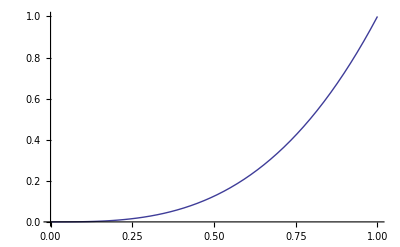

```mathematica
f[3]
List[f[1],f[2],f[3]]
D[( f[x]^2+x), x]
Plot[f[x],{x,0,1}, PlotRange->All]
```

NOTICE: Four commands, simultaneously entered, produced four distinctly numbered outputs.

NOTE the use of the subscripted _ to identify the "independent variable" x. Its purpose becomes clearer when you look at

```mathematica
f[x_,y_]:=u x^3+v y^3 +w
```

where we have announced our intention to look upon x, y as variables, and u, v, w as adjustable constants/parameters. The command

```mathematica
D[f[x,y], x]
```

3 u x^2

gave a result that is not at all surprising. But the result produced by the command

```mathematica
D[f[x,y], u]
```

x^3

is a little bit surprising: Mathematica has uncomplainingly differentiated with respect to a parameter.

### Piece-wise Functional Definition

We sometimes encounter functions that are defined "piece-wise."

EXAMPLE: I have in mind a "vee-shaped" function, that I will call vee[x]:

```mathematica
vee[x_]:=1 /; x<-1  
vee[x_]:=-x /; -1<x<0
vee[x_]:=+x /; 0<x<1
vee[x_]:=1 /; 1<x
```

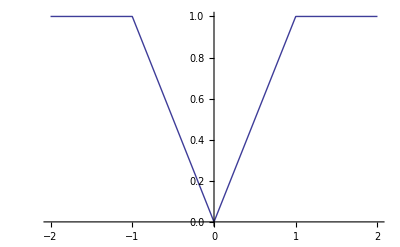

```mathematica
Plot[vee[x],{x,-2,2}]
```

NOTE the use of the symbolic construction /;, which means "use this rule when the following test is True."

Mathematica 6 provides a command that does the same job a bit more simply…

```mathematica
?Piecewise
```

Piecewise[{{val_1,cond_1},{val_2,cond_2},…}] represents a piecewise function with values val_i in the regions defined by the conditions cond_i. 
Piecewise[{{val_1,cond_1},…},val] uses default value val if none of the cond_i apply. The default for val is 0.

…as I now illustrate:

```mathematica
newvee[x_]:=Piecewise[{{1,x<-1},{-x,-1<x<0},{+x,0<x<1},{1,1<x}}]
```

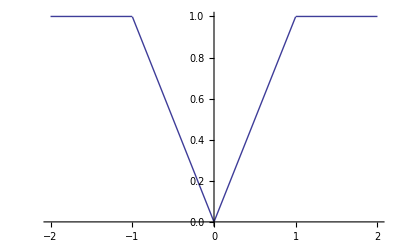

```mathematica
Plot[newvee[x], {x, -2, 2}]
```

Here we  compute the derivative of newvee[x]:

```mathematica
D[newvee[x],x]
```

Piecewise[{{0, x<-1}, {-1, -1<x<0}, {1, 0<x<1}, {0, x>1}, {Indeterminate, True}}]

An important instance of such a function is the Heaviside  UnitStep function, which is a built-in resource of Mathematica and usually plays a role very like that of an on/off switch:

```mathematica
?UnitStep
```

RowBox[{"UnitStep", "[", StyleBox["x", "TI"], "]"}] represents the unit step function, equal to 0 for RowBox[{"x", "<", "0"}] and 1 for RowBox[{"x", "≥", "0"}]. 
RowBox[{"UnitStep", "[", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] represents the multidimensional unit step function which is 1 only if none of the SubscriptBox["x", "i"] are negative.

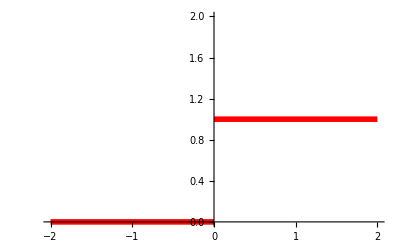

```mathematica
Plot[UnitStep[x],{x,-2,2},PlotStyle->{{RGBColor[1,0,0],Thickness[0.01]}}, PlotRange->{0,2}]
```

### Equality Tests

When you intend "equals" in the familiar sense, Mathematica hears you either to be asking a question (are the expressons on left and right equal? to which Mathematica will respond either True or False) or to be stipulating that the expressions on left and right are equal. In either Mathematica expects you to write ==.  Here are some simple examples:

```mathematica
2+2==3
2+2==4
```

False

True

```mathematica
Solve[ϕ^2-ϕ-1==0]
```

{{ϕ→1/2 (1-√5)},{ϕ→1/2 (1+√5)}}

We ask for the numerical values of those expressions

```mathematica
N[%]
```

{{ϕ→-0.618034},{ϕ→1.61803}}

and observe that the positive root of the equation in question is precisely the "golden ratio":

```mathematica
N[GoldenRatio]
```

1.61803

### Secondary Flavors of = , and of Some of its Relatives

Constructions like === and =!= (its negation), <, >, <= and => return True/False as output, and are used mainly in Mathematica programing. The first asks whether the expressions on left and right are structurally identical:

```mathematica
3 x^2===D[x^3, x]
```

True

```mathematica
Sin[x]^2+Cos[x]^2===1
Sin[x]^2+Cos[x]^2=!=1
```

False

True

In the latter instance we have equality but not structural identity.

For more information, go to Help > Documentation Center and in the search window at the top of the page ask for "Conditionals."

## Clear

Open a new notebook, enter f[u] and discover that the definition introduced a while ago is still in force.  It lives in the Kernel, and so will travel with you from notebook to notebook until either you explicitly discard it or terminate this work session; i.e., until either you  Clear the definition or Quit  Mathematica.  Now close and discard your nameless new notebook.

Relatedlyt: suppose you had interest at this point in defining

```mathematica
distance[t_]:=r+1/2 g t^2
```

To check to see what you have created (always a good idea!), command

```mathematica
distance[t]
```

r+(t^2 -Graphics-)/2

and get something weird.  That is because you have previously assigned a meaning to g, and that assignment is still lively:

```mathematica
Show[g]
```

-Graphics-

You might reassign meaning to the symbols f[x] and g, but how do you simply strip away the meanings they have previously acquired;  how do you restore them to the list of undefined symbols? For this purpose Mathematica provides the command Clear.

```mathematica
?Clear
```

Clear[symbol_1,symbol_2,…] clears values and definitions for the symbol_i. 
Clear[form,form,…] clears values and definitions for all symbols whose names match any of the string patterns form_i.

To see how this works, command

```mathematica
Clear[g]
```

and see that g is now once again just a letter in the alphabet:

```mathematica
g
```

g

It is, in particular, no longer the name of a graph:

```mathematica
Show[g]
```

Show::gtype: Symbol is not a type of graphics.

Show[g]

What about the removal of the function f[x]? The command

```mathematica
?f
```

Global`f

f[x_]:=x^17
 
f[x_,y_]:=u x^3+v y^3+w

reminds us that we have in fact—carelessly—taken f to be the name of two distinct functions. The command

```mathematica
Clear[f]
```

simultaneously expunges ALL the meanings we have previously associated with the letter f, as we now demonstrate:

```mathematica
f[x]
f[x,y]
```

f[x]

f[x,y]

It is to avoid this difficulty that one must be careful to assign distinct names to all functions. In  the present instance we might more wisely have written (say)

```mathematica
f1[x_]:=x^17
f2[x_,y_]:=u x^3+v y^3+w
```

We check those definitions

```mathematica
f1[x]
f2[x,y]
```

x^17

w+u x^3+v y^3

and verify that

```mathematica
Clear[f1]
```

expunges the former, but not the latter:

```mathematica
f1[x]
f2[x,y]
```

f1[x]

w+u x^3+v y^3

TIP: One should be careful to clear assignments/definitions when you are finished with them. This frees up memory, and helps avoid distracting surprises and confusion. But you will sometimes forget, so…

TIP: It is a good idea to make Clear[the symbols you plan to use] your first command when, in the midst of a work session, you start a fresh computation.

We will have no immediate need of this more comprehensive command:

```mathematica
?ClearAll
```

ClearAll[symb_1,symb_2,…] clears all values, definitions, attributes, messages and defaults associated with symbols. 
ClearAll[form,form,…] clears all symbols whose names textually match any of the form_i.

#### How to Clear a Subscripted Variable

Suppose you have had occasion to define

```mathematica
Subscript[a, 3]=SomeExpression
```

SomeExpression

and want now to clear a_3. The command

```mathematica
Clear[Subscript[a, 3]]
```

Clear::ssym: a_3 is not a symbol or a string.

did not work. Nor does it work to command

```mathematica
Clear[a]
```

for we still have

```mathematica
Subscript[a, 3]
```

SomeExpression

How to proceed? Vacate the definition by defining a_3 to be "nothing," this way:

```mathematica
Subscript[a, 3]=.
```

Test the result:

```mathematica
Subscript[a, 3]
```

a_3

## Sources of Information

### Hardcopy Materials

Earlier versions of Mathematica shipped with hardcopy editions of

• The Mathematica Book, which provided definitive descriptions of every feature of the software, but was much too fat to carry around. Chapter I "A Practical Introduction to Mathematica" ran to 228 pages, and provided a valuable survey of the basics, with many examples.

• Mathematica Standard Add-on Packages, which described and illustrated tyhe use of roughly 1000 resources—many quite valuable—which were installed together with Mathematica, but became available only when explicitly called upon.

The release of v.6 has rendered those books obsolete, but not entirely, and has actually increased their value, for with the release of v.6 Wolfram seems to have elected to discontinue the preparation/distribution of such volumes: all such information must now be sought electronically, by consulting resources accessed via the Help menu.

A great many books by authors not associated with Wolfram are available in the market place—visit  —but most of those are similarly obsolete. Of those, some are addressed to students, others to experts; some provide tutorial overviews, others threat specialized topics (differential equations, graphics, statistics, etc.).

REMARK: To insert the link into that sentence, I used a resouce you can read about if you command

```mathematica
?Hyperlink
```

Hyperlink[uri] represents a hyperlink that jumps to the specified URI when clicked. 
Hyperlink[label,uri] represents a hyperlink to be displayed as label.

and follow the ». More specifically, I entered (in a notebook I am using as "scratch paper") the command

```mathematica
Hyperlink["WolframBooks","http://store.wolfram.com/catalog/books/author.html"]
```

and then Copy/Pasted the output into this notebook into the sentence where you found it. Note carefully that, while it might be most natural to type "WolframBooks," the command will not function unless you type "WolframBooks",

The Mathematica Journal appears monthly, reads much like American Journal of Physics or Mathematical Monthly (so is, for the most part, readily accessible to students), and is available in the Reed College Library.

### Built-in Sources

The primary source of information about v.6 is provided now by Help > Documentation Center, but it is like a Chinese box—arrays of links to arrays of links to arrays of links…  I cannot possibly present a map or those resources, urge you to spend some time exploring on your own to try to gain a vague sense of the lay of the land. You might, in particular, do this non-obvious thing: type Standard Packages in the search window. That will take you to 30 pages of stuff. Now type Physical Constants in the search window, click on Physical Constants Package (Physical Constants Package Tutorial): that will provide indication of the resources that become available once that particular package is installed, and instructions about how to install it. We are told to command

```mathematica
<<PhysicalConstants`
```

and that we will then have access to information such as the following:

```mathematica
ClassicalElectronRadius
```

2.81794×10^-15 Meter

```mathematica
SpeedOfLight
```

(299792458 Meter)/Second

But there exist other/quicker ways to obtain information which are frequently quite useful. Suppose, for example, that we had computed

```mathematica
∑_(j=0)^∞ x^j/(j+u)^ν
```

LerchPhi[x,ν,u]

and find ourselves wondering "What in the world is a 'LerchPhi function'?" We might enter

```mathematica
?LerchPhi
```

LerchPhi[z,s,a] gives the Lerch transcendent Φ(z,s,a).

which gives us some little information, and if we enter

```mathematica
??LerchPhi
```

LerchPhi[z,s,a] gives the Lerch transcendent Φ(z,s,a).

Attributes[LerchPhi]={Listable,NumericFunction,Protected,ReadProtected}
 
Options[LerchPhi]={DoublyInfinite→False,IncludeSingularTerm→False}

or equivalently

```mathematica
Information[LerchPhi]
```

LerchPhi[z,s,a] gives the Lerch transcendent Φ(z,s,a).

Attributes[LerchPhi]={Listable,NumericFunction,Protected,ReadProtected}
 
Options[LerchPhi]={DoublyInfinite→False,IncludeSingularTerm→False}

we get more detailed information—some of it pretty cryptic. But—backing up to our starting point—if in

LerchPhi[x,ν,u]

we Select the output (select only the LerchPhi; leave out the [x,ν,u]) and then open Help > Find Selected Function… we are instantly led to a notebook that provides a detailed description of the "Lerch transcendent" and of its relation to (among others) the Riemann zeta and polylog functions.

Under TUTORIALS (near the bottom of the page), open and explore the link to the very valuable Special Functions notebook.

Distinct from Information is Options. We will ask Mathematica itself to describe the difference:

```mathematica
?Information
?Options
```

Information[symbol] prints information about a symbol.

RowBox[{"Options", "[", StyleBox["symbol", "TI"], "]"}] gives the list of default options assigned to a symbol. 
RowBox[{"Options", "[", StyleBox["expr", "TI"], "]"}] gives the options explicitly specified in a particular expression such as a graphics object. 
RowBox[{"Options", "[", StyleBox["stream", "TI"], "]"}] or RowBox[{"Options", "[", StyleBox["\"\!\(\*StyleBox[\"sname\",\"TI\"]\)\"", ShowStringCharacters->True], "]"}] gives options associated with a particular stream. 
RowBox[{"Options", "[", StyleBox["object", "TI"], "]"}] gives options associated with an external object such as a NotebookObject. 
RowBox[{"Options", "[", RowBox[{StyleBox["obj", "TI"], ",", StyleBox["name", "TI"]}], "]"}] gives the setting for the option StyleBox["name", "TI"]. 
RowBox[{"Options", "[", RowBox[{StyleBox["obj", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["name", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["name", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives a list of the settings for the options SubscriptBox[StyleBox["name", "TI"], StyleBox["i", "TI"]].

Many things—graphics most notoriously—support lots of options. Suppose, for example, we perform

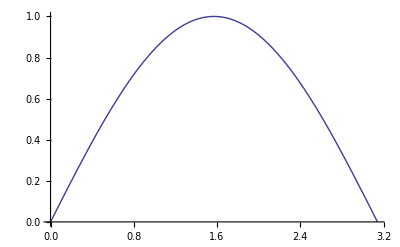

```mathematica
Plot[Sin[x],{x,0,π}]
```

and then become curious about the options which were available to us; to discover those, we enter

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

What to do with such information? Again, ask Mathematica. Which, for example, about the AlignmentPoint option has this to say:

```mathematica
Information[AlignmentPoint]
```

AlignmentPoint is an option which specifies how objects should by default be aligned when they appear in Inset.

Attributes[AlignmentPoint]={Protected}

Here as always, if you follow the » you will be led to detailed discussion and examples.

### Your Own "My Tricks" Notebook

I mention finally an undocumentable resource which will in time become the most valuable of all. Experience is problem-solving, in this sphere as in all others.  When Mathematica has presented difficulties which you have finally overcome (it will, and you will), take the time to record your success in a dedicated notebook. You will then never again have to solve that particular problem, and can use your former success as a Copy/Paste template. For your

```mathematica
Mathematica power=∑_(t=today)^tomorrow Problems successfully solved
```

And don't be too proud to save also—perhaps in a separate notebook of  "Stolen Tricks"—a record of the ideas developed by others that seem to you interesting, or potentially useful. Quite a number of those will be encountered as  we proceed.

Sometimes your "tricks" will consist of programs that run a dozen or more lines (Mathematica programs are seldom very long; that heavy work was done by the designers of the software), but more often they will consist of felicitous selections from among available options. The value of your Tricks Notebooks will be much increased if you include explanatory text and references—easy if you open Window > Show Toolbar. Notice also that you need not add to the end of your notebook: you can introduce new material interstitially, in conformity with some organizational pattern, with categories labled with appropriate Section titles.

Use Mathematica's Edit > Find command, or OSX's Spotlight, to locate material in your notebooks.  The task is made easier if you embellish your notebooks with appropriate tag words and phrases.

## Memory Management

If you have interest in how much memory you have used in this work session (prior to the development of OSX that was always a critical consideration, since Mathematica tends to consume lots of memory, and in pre-OSX days memory management was not automatic), command

```mathematica
MaxMemoryUsed[]
```

9515416